```mathematica
p[z_]:=PDF[MultinormalDistribution[μ,σ],z]
```

```mathematica
w[z_]:=PDF[NormalDistribution[θ,ω],z]
```

```mathematica
Integrate[p[z]w[z],{z,-∞,∞},Assumptions->{σ>0,ω>0}]
```

(ⅇ^(-(θ-μ)^2/(2 (σ^2+ω^2))))/(√(2 π) √(σ^2+ω^2))

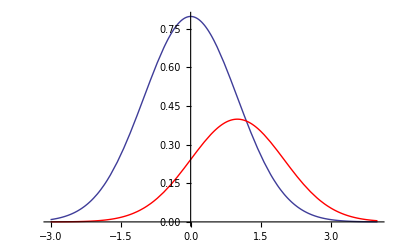

```mathematica
Show[
Plot[2*PDF[NormalDistribution[θ,ω],z]/.θ->0/.ω->1,{z,-3,4}],
Plot[PDF[NormalDistribution[μ,σ],z]/.μ->1/.σ->1,{z,-3,4},PlotStyle->Red]
]
```

```mathematica
D[(ⅇ^(-(θ-μ)^2/(2 (σ^2+ω^2))))/(√(2 π) √(σ^2+ω^2)),σ]//FullSimplify
```

(ⅇ^(-(θ-μ)^2/(2 (σ^2+ω^2))) σ ((θ-μ)^2-σ^2-ω^2))/(√(2 π) (σ^2+ω^2)^(5/2))

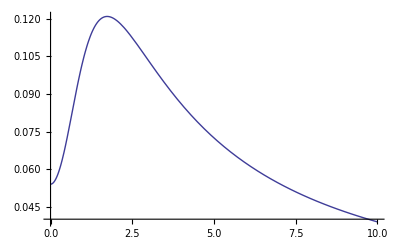

```mathematica
Plot[(ⅇ^(-(θ-μ)^2/(2 (σ^2+ω^2))))/(√(2 π) √(σ^2+ω^2))/.ω->1/.θ-> 0/.μ->2,{σ,0,10}]
```